```mathematica
ClearAll["Global`*"]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/PATH TO REPOSITORY FOLDER"}]
```

```mathematica
tt =α/(v*(ρ*μ)/β*α/n)
```

(n β)/(v μ ρ)

```mathematica
tt = 1/ρ*(n0*β0)/(μ*v0)*M^0.08/.(n0*β0)/(μ*v0)->tt0
```

(M^0.08 tt0)/ρ

```mathematica
tb = tb0*M^0.124
tc = tc0*M^0.196
```

M^0.124 tb0

M^0.196 tc0

```mathematica
ne = (tb*1/tc)/(tt*1/tc+tc*1/tc)
```

tb0/(M^0.072 tc0 (1.+tt0/(M^0.116 tc0 ρ)))

```mathematica
maxgut = ϵ*g0*M^0.897
```

g0 M^0.897 ϵ

```mathematica
costs = c0*M^-0.626
```

c0/M^0.626

```mathematica
LogDerivative[f_,x_]:=FullSimplify[D[Log[f],x]*x]
```

```mathematica
ExpD= (α*β*(n/(w*h))^(ζ-1))/(μ*(α*(n/(w*h))^(ζ-2)-1))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1}
```

(M^β1 ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) α β0)/((-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ExpVolume= (α*β*(n/(w*h))^(ζ-1))/(μ*(α*(n/(w*h))^(ζ-2)-1))*w*h/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1}
```

(h0 M^(h1+w1+β1) ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) w0 α β0)/((-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ttravel = (α*β*(n/(w*h))^(ζ-1))/(v*μ*(α*(n/(w*h))^(ζ-2)-1))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
v->v0*M^v1,
w->w0*M^w1,
h->h0*M^h1}
```

(M^(-v1+β1) ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) α β0)/(v0 (-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ttravelVAR=(1/v)^2*((α*(n/(w*h))^(ζ-2))^3)/((μ/(β*(n/(w*h))))^2*(α*(n/(w*h))^(ζ-2)-1)^2*(α*(n/(w*h))^(ζ-2)-2))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
v->v0*M^v1,
w->w0*M^w1,
h->h0*M^h1}
```

(M^(-2 h1-2 v1-2 w1+2 β1) (1+2 M^(n1+tb1+v1) n0 tb0 v0)^2 ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-6+3 ζ) α^3 β0^2)/(h0^2 v0^2 w0^2 (-2+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) (-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α)^2 μ^2)

```mathematica
(*ttravel = 1/μ*(β0*M^β1*α*(n0*M^(n1)*(a0*M^(a1)))^(ζ-1))/(v0*M^v1*w0*M^w1*h0*M^h1*(α*(n0*M^(n1)*(a0*M^(a1)))^(ζ-2)-1))/.{a0->2*v0*tb0,a1->v1+tb1}*)
```

```mathematica
(*ttravel = (β0*M^β1*α*(n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1)))^(ζ-1))/(v0*M^v1*w0*M^w1*h0*M^h1*(α*(n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1)))^(ζ-2)-1))*)
```

```mathematica
ttravelParam = FullSimplify[ttravel/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}]
```

(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)

```mathematica
ttravelVARParam = FullSimplify[ttravelVAR/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}]
```

(7.10164×10^-6 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.297333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ^2)

```mathematica
ExpDParam= ExpD/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}
```

(0.002 0.666223^(-1+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-1+ζ) M^0.969 α)/((-1+0.666223^(-2+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-2+ζ) α) μ)

```mathematica
ExpVolumeParam = ExpVolume/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}
```

(0.003002 0.666223^(-1+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-1+ζ) M^1.65933 α)/((-1+0.666223^(-2+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-2+ζ) α) μ)

```mathematica
zetavec = {1,1.5,2,2.15}
```

{1,1.5,2,2.15}

```mathematica
CompetitiveLoad=n/(w*h)/.{n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1};
CompetitiveLoadParam = CompetitiveLoad/.{v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124};
```

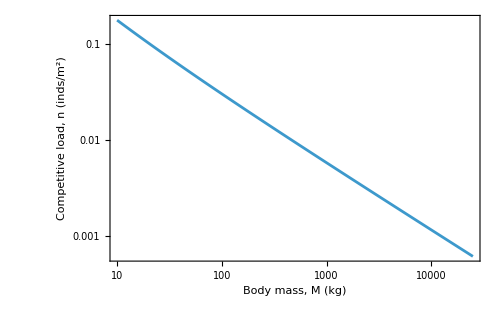

```mathematica
CompPlot = LogLogPlot[CompetitiveLoadParam,{M,10,25000},Frame->True,FrameLabel->{"Body mass, M (kg)","Competitive load, n (inds/m^2)"},LabelStyle->Directive[FontSize->16],ImageSize->500]
```

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_compload.pdf"],CompPlot]
```

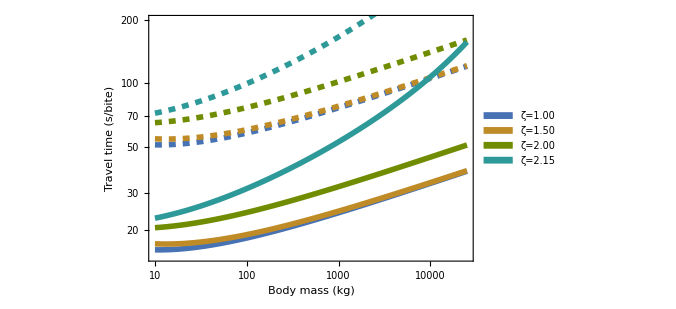

```mathematica
CD = 86;
PlotTravel = Show[
Flatten[{
LogLogPlot[ttravelParam/.{μ->10^-4,α->4,ζ->zetavec[[1]]},{M,10,25000},PlotRange->{15,200},PlotStyle->Directive[Thickness[0.008],Dashed,ColorData[CD,1]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16],PlotLegends->SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3],ColorData[CD,4]},{"ζ=1.00","ζ=1.50","ζ=2.00","ζ=2.15"}]],
Table[
LogLogPlot[ttravelParam/.{μ->10^-4,α->4,ζ->zetavec[[i]]},{M,10,25000},PlotStyle->Directive[Thickness[0.008],Dashed,ColorData[CD,i]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16]]
,{i,2,Length[zetavec]}],
Table[
LogLogPlot[ttravelParam/.{μ->10^-3.5,α->4,ζ->zetavec[[i]]},{M,10,25000},PlotStyle->Directive[Thickness[0.008],ColorData[CD,i]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16]]
,{i,1,Length[zetavec]}]
},1]
,ImageSize->500
]
```

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_traveltime.pdf"],PlotTravel]
```

```mathematica
(*1) Define a robust converter that handles any ColorData output*)
colorToHex[color_]:=Module[
{rgb},(*force an RGB representation*)
rgb=List@@ColorConvert[color,"RGB"];
"#"<>StringJoin[IntegerString[Round[255 #],16,2]&/@rgb]];

(*2) Pull out the first three swatches from palette 86*)
Table[colorToHex[ColorData[86][i]],{i,1,5}]
```

{#4772b2,#bf8b26,#708c00,#2e9999,#8167e6}

```mathematica
i = 4; {ColorData[97,i],colorToHex[ColorData[97,i]]}
```

{RGBColor[0.922526, 0.385626, 0.209179],#eb6235}

```mathematica
nefullParam = FullSimplify[(tb0*M^tb1)/(ttravelParam+(tc0*M^tc1)*(β0*M^β1))/.{
β0->0.002,
β1->0.969,
tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196
}]
```

(18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
nefullDeltaParam = (tb0*M^tb1)/(ttravelParam+(tc0*M^tc1)*(β0*M^β1))+ 1/2*(2*(tb0*M^tb1))/((ttravelParam+(tc0*M^tc1)*(β0*M^β1))^3)*ttravelVARParam/.{
β0->0.002,
β1->0.969,
tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196
}
```

(18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.129392 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.421333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^3 μ^2)

```mathematica
nefullParam/.{μ->10^-4,α->3,M->10000}
```

57088.5/(24.3811+(272384. 0.00116357^(-1+ζ))/(-1+3 0.00116357^(-2+ζ)))

```mathematica
neValues = Table[{10^i,nefullParam/.{μ->10^-2,α->4,ζ->1,M->10^i}},{i,4,4.5,0.1}];
(*Assume neValues is defined as in your code*)
logNeValues=Log10@neValues;
(*Fit a linear model to the log-log data*)
fit=LinearModelFit[logNeValues,x,x]
(*Extract the slope*)
slope=fit["BestFitParameters"][[2]]
int = fit["BestFitParameters"][[1]]
```

FittedModel[…]

-1.01596

7.41591

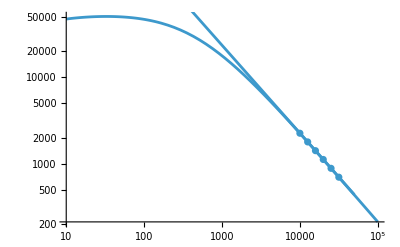

```mathematica
Show[
LogLogPlot[nefullParam/.{μ->10^-2,α->4,ζ->1},{M,10,10^5}],
ListLogLogPlot[neValues],
LogLogPlot[10^int*M^slope ,{M,10,50000}]
]
```

```mathematica
gainsParam = nefullParam*(β0*M^β1)*ϵ/.{β0->0.002,β1->0.969,ϵ->18.2}
```

(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
gainsDeltaParam = nefullDeltaParam*(β0*M^β1)*ϵ/.{β0->0.002,β1->0.969,ϵ->18.2}
```

0.0364 M^0.969 ((18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.129392 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.421333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^3 μ^2))

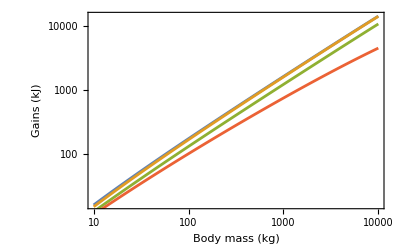

```mathematica
Show[
Table[
LogLogPlot[gainsParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Gains (kJ)"}],
{i,1,Length[zetavec]}]
]
```

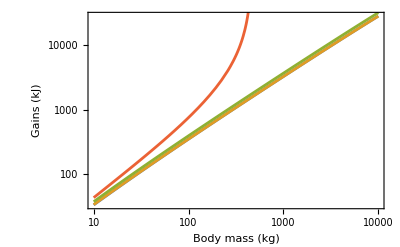

```mathematica
Show[
Table[
LogLogPlot[gainsDeltaParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Gains (kJ)"}],
{i,1,Length[zetavec]}]
]
```

```mathematica
costsParam = nefullParam*ttravelParam*(F0*M^F1) + nefullParam*(tc0*M^tc1)*(B0*M^B1) + tday*(B0*M^B1) - (tb0*M^tb1)*(B0*M^B1)/.{tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196,
F0->0.0084,(*0.001 kJps * f0_g * (1000)^(0.75)*)
F1->0.75,
B0->0.0032,(*0.001 kJps * b0_g * (1000)^(0.75)*)
B1->0.75,
tday -> 24*60*60}
```

276.48 M^0.75-58.304 M^0.874+(15.5497 M^1.07)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.612192 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^1.713 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)) μ)

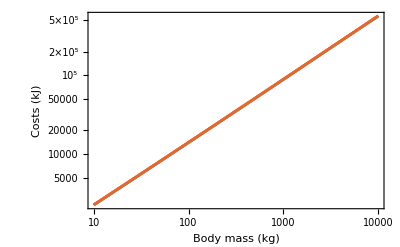

```mathematica
Show[
Table[
LogLogPlot[costsParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
{i,1,Length[zetavec]}]
]
```

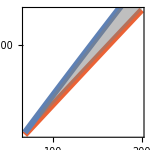

```mathematica
muExp = -3.06;
insetPlot = Show[
LogLogPlot[costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,80,200},PlotStyle->Directive[Thickness[0.03],ColorData[97,4]],Frame->True,FrameTicks->None,(*FrameLabel->{"Body mass (kg)","Gains,  Costs (kJ)"},*)LabelStyle->Directive[FontSize->16],FrameStyle->Directive[Black,Thick]],
LogLogPlot[gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,80,200},PlotStyle->Directive[Thickness[0.03],ColorData[97,1]],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
LogLogPlot[{costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]}},{M,90,200},PlotStyle->Transparent,Filling->{1->{{2},{Directive[Gray,Opacity[0.5]]}}}]
, AspectRatio->1,ImageSize->150
]
```

```mathematica
simgaincost = Import[StringJoin[namespace,"/data/simdata/gaincostpoor_data.csv"]][[2;;All]];
```

```mathematica
simgain = Transpose[{simgaincost[[All,1]],simgaincost[[All,2]]}];
simcost = Transpose[{simgaincost[[All,1]],simgaincost[[All,3]]}];
```

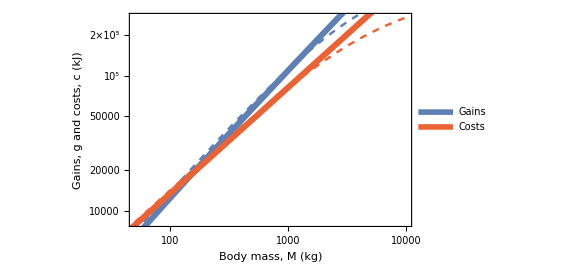

```mathematica
PlotGainCost=Legended[Show[
muExp = -3.1;
LogLogPlot[costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[97,4]],Frame->True,FrameLabel->{"Body mass, M (kg)","Gains, g and costs, c (kJ)"},LabelStyle->Directive[FontSize->16,Black],FrameStyle->Black(*,PlotLegends->LineLegend[{ColorData[97,1],ColorData[97,4]},{"Gains","Costs"}]*)],
LogLogPlot[gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[97,1]],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
ListLogLogPlot[simgain,PlotStyle->Directive[Thickness[0.01],ColorData[97,1]],Joined->True],
ListLogLogPlot[simcost,PlotStyle->Directive[Thickness[0.01],ColorData[97,4]],Joined->True]
,ImageSize->435],
Placed[LineLegend[{Directive[ColorData[97,1],Thickness[0.02]],Directive[ColorData[97,4],Thickness[0.02]]},{"Gains","Costs"},LegendMarkerSize->14,LabelStyle->Directive[FontSize->14]],Scaled[{0.1,0.875}]]
]
```

```mathematica
gainsValues = Table[{10^i,gainsParam/.{μ->10^-5,α->4,ζ->1,M->10^i}},{i,3,4.5,0.1}];
(*Assume neValues is defined as in your code*)
loggainsValues=Log10@gainsValues;
(*Fit a linear model to the log-log data*)
fit=LinearModelFit[loggainsValues,x,x]
(*Extract the slope*)
slope=fit["BestFitParameters"][[2]]
```

FittedModel[…]

0.933121

```mathematica
gainslope = LogDerivative[gainsParam,M]
```

1/M^0.093 0.00150782 ((724.886 M^0.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))-(663.208 M^1.093 (0.000621411 M^0.165+(0.003356 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) α)/(M^0.161 (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)-(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(2 (-2+ζ)) M^0.839 α^2 (-2+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ)+(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) M^0.839 α (-1+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^2) (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
gainscostsratioParam = gainsParam/costsParam;
```

```mathematica
simgaincostzeta10 = Import[StringJoin[namespace,"/data/simdata/gaincostpoor_zeta1_data.csv"]][[2;;All]];
simgaincostzeta15 = Import[StringJoin[namespace,"/data/simdata/gaincostpoor_zeta15_data.csv"]][[2;;All]];
simgaincostzeta20 = Import[StringJoin[namespace,"/data/simdata/gaincostpoor_zeta20_data.csv"]][[2;;All]];
simgaincostzeta215 = Import[StringJoin[namespace,"/data/simdata/gaincostpoor_zeta215_data.csv"]][[2;;All]];
```

```mathematica
simgainzeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,2]]}];
simcostzeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,3]]}];
simgainzeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,2]]}];
simcostzeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,3]]}];
simgainzeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,2]]}];
simcostzeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,3]]}];
simgainzeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,2]]}];
simcostzeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,3]]}];
```

```mathematica
simgaincostratiozeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,2]]/simgaincostzeta10[[All,3]]}];
simgaincostratiozeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,2]]/simgaincostzeta15[[All,3]]}];
simgaincostratiozeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,2]]/simgaincostzeta20[[All,3]]}];
simgaincostratiozeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,2]]/simgaincostzeta215[[All,3]]}];
```

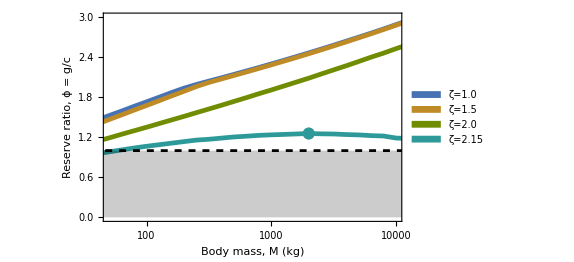

```mathematica
CD = 86;
PlotGainsCostsRatioZeta = Show[
ListLogLinearPlot[simgaincostratiozeta10,PlotStyle->Directive[Thickness[0.008],ColorData[86,1]],Joined->True,Frame->True,FrameLabel->{"Body mass, M (kg)","Reserve ratio, ϕ = g/c"},PlotRange->{{50,10000},{0,3}},LabelStyle->Directive[Black,FontSize->16],PlotLegends->Placed[SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3],ColorData[CD,4]},{"ζ=1.0","ζ=1.5","ζ=2.0","ζ=2.15"}],{Scaled[{0.01,0.80}], {0, 0.5}}]],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->1},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,4]]],*)

ListLogLinearPlot[simgaincostratiozeta15,PlotStyle->Directive[Thickness[0.008],ColorData[86,2]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->1.5},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,2]]],*)

ListLogLinearPlot[simgaincostratiozeta20,PlotStyle->Directive[Thickness[0.008],ColorData[86,3]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->2},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,3]]],*)

ListLogLinearPlot[simgaincostratiozeta215,PlotStyle->Directive[Thickness[0.008],ColorData[86,4]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->2.15},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,4]]],*)

LogLinearPlot[1,{M,10,50000},PlotStyle->Directive[Dashed,Black],Filling->Bottom],
ListLogLinearPlot[{simgaincostratiozeta215[[Position[simgaincostratiozeta215[[All,2]],Max[simgaincostratiozeta215[[All,2]]]][[1]][[1]]]]},PlotStyle->Directive[PointSize[0.02],ColorData[86,4]]], ImageSize->425
]
```

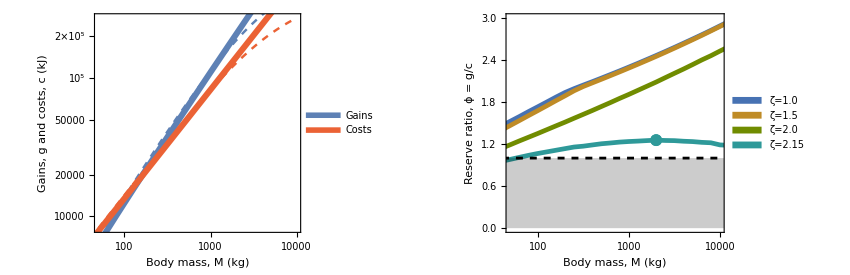

```mathematica
PlotGainRowV4 =GraphicsRow[{PlotGainCost,PlotGainsCostsRatioZeta},ImageSize->850,Spacings->1]
```

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_gainrowv4.pdf"],PlotGainRowV4]
```

/Users/jdyeakel/Dropbox/PostDoc/2025_fatscaling/fatscaling/rawfigures/fig_gainrowv4.pdf

```mathematica
gainremainderParam = gainsParam - c0*M^c1/.{c0->Exp[5.86],c1->0.79} (*Updated values 4/15/2025*)
```

-350.724 M^0.79+(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
gainremainderslope = LogDerivative[gainremainderParam,M]
```

(M (-277.072/M^0.21+(724.886 M^0.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))-(663.208 M^1.093 (0.000621411 M^0.165+(0.003356 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) α)/(M^0.161 (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)-(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(2 (-2+ζ)) M^0.839 α^2 (-2+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ)+(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) M^0.839 α (-1+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^2))/(-350.724 M^0.79+(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))

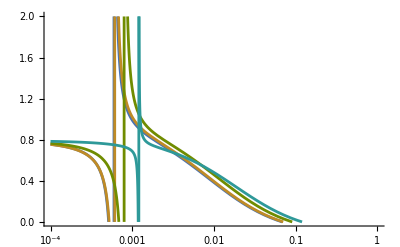

```mathematica
Show[
Table[
LogLinearPlot[gainremainderslope/.{M->500,α->4,ζ->zetavec[[i]]},{μ,10^-4,10^0},PlotRange->{0,2},PlotStyle->ColorData[86,i]],
{i,1,Length[zetavec]}]
(*,
LogLinearPlot[0.788,{μ,10^-5,10^0},PlotStyle->Directive[Dashed,Black]]*)
]
```

```mathematica
gainremainderslopeValues = Table[{10^i,gainremainderslope/.{M->500,α->4,μ->10^i,ζ->1}},{i,-3.5,0,0.01}];
```

```mathematica
Export[StringJoin[namespace,"/data/simdata/expgainremainderslope.CSV"],gainremainderslopeValues]
```